```mathematica
CloseStreams[];ArrayPlot[
Table[
Table[{p,RatioFor[tuple,{p}]}, {p, tuple}]
,{tuple, Subsets[Prime[Range[2,25]],{2}]}
]
,
PlotRange->All,
GridLines->{Automatic,Append[Table[t,{t,0,1,0.1}],{0.45,{Red,Thick}}]},
Frame->True,
ImageSize->1000
]
```

```mathematica
Needs["Polytopes`"]
```

Needs[Polytopes`]

```mathematica
Needs["Polytopes`"]
```

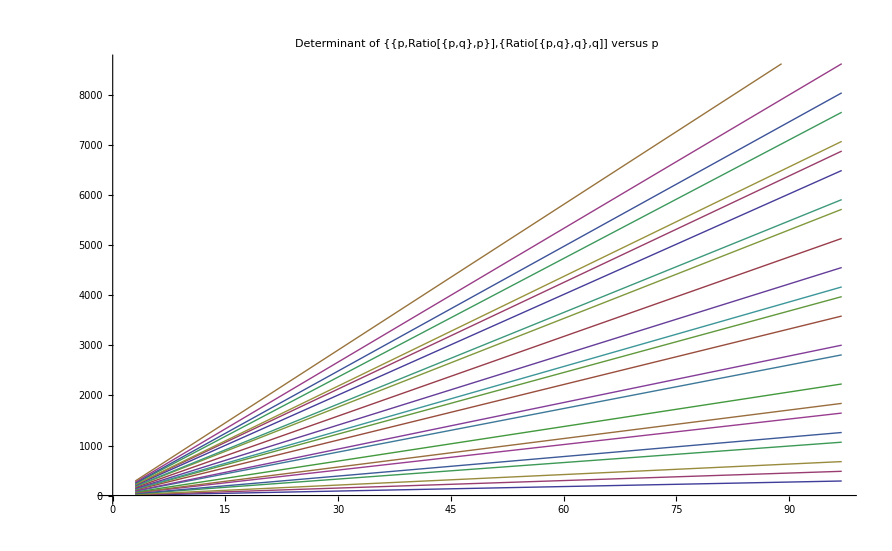

Creating directory d:\triangle\Votes\main\p

```mathematica
CloseStreams[];
ListLinePlot[
Table[
Table[{p,Det[MatrixForm[{{q,RatioFor[Sort[{q,p}],{q}]},{RatioFor[Sort[{q,p}],{p}],p }}]]},
{p, Select[Prime[Range[2,25]],# ≠ q&]}
]
,{q,Prime[Range[2,25]]}
],
PlotMarkers->None,
PlotLabel->"Determinant of {{p,Ratio[{p,q},p}],{Ratio[{p,q},q},q]] versus p"
]
```

```mathematica
Solve[Det[{{p,a},{b,q}}]==v, a]
```

{{a→(p q-v)/b}}

```mathematica
PrimePi[139]
```

34

```mathematica
Area[{{61,0.908485},{3,0.645355},{183,0.5632159999999999}}]
```

```mathematica
Area[{{61,0.908485},{3,0.645355},{183,0.5632159999999999}}]
```

Area[{{61,0.908485},{3,0.645355},{183,0.563216}}]

```mathematica
d= Polygon[{61,0.908485},{3,0.645355},{183,0.5632159999999999}]
```

Polygon[{61,0.908485},{3,0.645355},{183,0.563216}]

```mathematica
Area[d]
```

Area[Polygon[{61,0.908485},{3,0.645355},{183,0.563216}]]

```mathematica
MatrixForm[{{main,RatioFor[Sort[{main,p}],{main}]},{RatioFor[Sort[{main,p}],{p}],p }}]
```

(main | RatioFor[{main,p},{main}]
RatioFor[{main,p},{p}] | p)